# Wave Optics

La teoría de ondas contiene a la de rayos. La teoría de rayos es el limite de la teoría de ondas cuando la longitud de onda es infinitamente pequeña.

## Se define la ecuación de onda en 2 dimensiones

```mathematica
c0=299792458; n=1;
c[n_]= c0/n; (*velocidad de la luz en un medio con indice refractivo n*)
cc=1;
Lap[u_]:=D[u[t,x, y], {x,2}]+D[u[t,x, y], {y,2}];
(*Se define ecuacion de onda *)
weq=Lap[u] -1/cc^2 D[u[t,x,y],{t,2}]==0;
```

## Condiciones Iniciales

```mathematica
f[x_,y_]:=2 Exp[-(x^2+y^2)] +  Exp[-((x-2)^2+(y-2)^2)];
ic= u[0,x,y]==f[x,y] ;(*Se establecen condiciones iniciales*)
icd=Derivative[1,0, 0][u][0,x, y]==0;
```

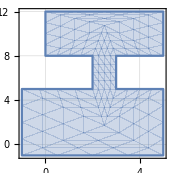

-Graphics3D-

```mathematica
dom = RegionUnion[Rectangle[{-1, -1}, {5, 5}],Rectangle[{2, 4}, {3, 8}], Rectangle[{0,8}, {5, 12}]];
RegionPlot[dom, GridLines->Automatic]
Plot3D[f[x,y], {x,y}∈dom ,PlotRange->Full]
```

## Se Resuelve como un Problema de Valor Inicial

```mathematica
wave=NDSolveValue[{weq, ic, icd}, u, {t,0,30}, {x,y}∈ dom];
fWave=Table[Plot3D[wave[t,x,y], {x,y}∈wave["ElementMesh"], PlotRange->{-2, 3}, Boxed->False, Axes->False ], {t,0,30, 30/100}];
Manipulate[fWave[[i]], {{i,16,"time"},1,Length[fWave],1}, SaveDefinitions->True]
```